```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/nightmareforev/git/root_tracking/Mathematica/codes_from_anirban

## Required libraries and functions:

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
```

```mathematica
(*Run the following commands if MaTeX is not already installed and configured with Mathematica in your PC*)
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/usr/bin/pdflatex"
]*)
```

```mathematica
<<MaTeX`
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

## Architecture of the SRSPM:

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.7, la->1.2};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
(*b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;*)

b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

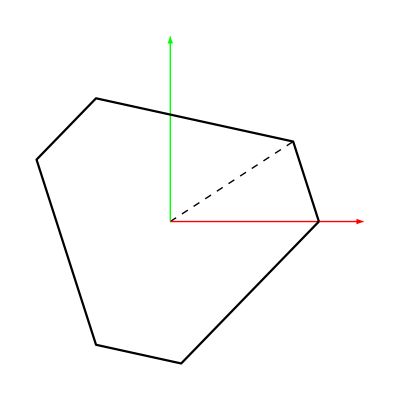

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

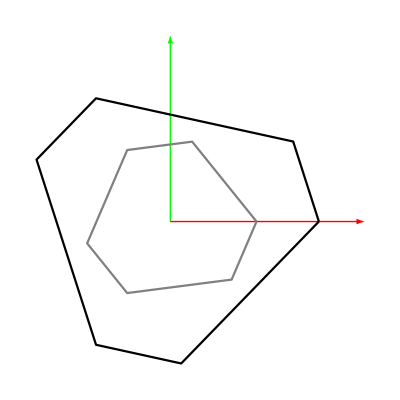

```mathematica
al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;

tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

```mathematica
cords = {"x", "y", "z"};
```

```mathematica
acords = Table[Table[Symbol["a"<>ToString[j]<>cords[[i]]],{i, 3}],{j, 6}]
```

{{a1x,a1y,a1z},{a2x,a2y,a2z},{a3x,a3y,a3z},{a4x,a4y,a4z},{a5x,a5y,a5z},{a6x,a6y,a6z}}

```mathematica
Inner[Rule, Flatten[acords], Flatten[b/.datap], List]
```

{a1x→1,a1y→0,a1z→0,a2x→0.827026,a2y→0.562164,a2z→0,a3x→-1/2,a3y→(√3)/2,a3z→0,a4x→-0.900361,a4y→0.435143,a4z→0,a5x→-1/2,a5y→-(√3)/2,a5z→0,a6x→0.0733353,a6y→-0.997307,a6z→0}

## Inverse Kinematics:

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*Now for the new coordinates the axes of the top platform is aligned to the global frame i.e., x axis is passes through the local a1*)
```

```mathematica
a1ptp = Simplify[(a[[1]]-ptp)/Sqrt[((b[[1]]).(b[[1]]))/.rb->rt/.γb->γt]];
```

```mathematica
a21 = Simplify[(a[[2]]-a[[1]])/Sqrt[(b[[2]]-b[[1]]).(b[[2]]-b[[1]])/.rb->rt/.γb->γt]];
```

```mathematica
sinangle = FullSimplify[(Cross[(b[[1]])/Sqrt[(b[[1]]).(b[[1]])], (b[[2]]-b[[1]])/Sqrt[(b[[2]]-b[[1]]).(b[[2]]-b[[1]])]]/.rb->rt/.γb->γt)][[3]];
```

```mathematica
zaxis = Simplify[Cross[a1ptp, a21]/sinangle];
Rtp = {a1ptp, Cross[zaxis, a1ptp], zaxis};
```

```mathematica
(*This is the relative rotation of the top platform now*)
```

```mathematica
rrmat = Rtp/.datap/.{ϕ1->-0.19338151566668343,ϕ2->-0.29196911634815836,ϕ3->0.46075322407379354,ϕ4->0.4607532240737936,ϕ5->-0.29196911634815814,ϕ6->-0.19338151566668318,ψ1->0.4241340724680215,ψ2->0.3655368415819105,ψ3->-0.054107411293902584,ψ4->0.05410741129390259,ψ5->-0.3655368415819105,ψ6->-0.4241340724680214,l1->1.1180592109777598,l2->1.11805921097776,l3->1.1180592109777598,l4->1.11805921097776,l5->1.1180592109777598,l6->1.1180592109777598}//Chop
```

{{1.38579,-0.792895,0},{0.907701,1.58644,0},{0,0,1.14479}}

```mathematica
rrmat.Transpose[rrmat]//Chop
```

{{2.54908,0,0},{0,3.34071,0},{0,0,1.31055}}

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
(*Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]*)
```

```mathematica
(*Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;*)
```

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
η1 = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
```

```mathematica
ηconfig = η1/.datap/.leglparam/.legmparam/.tpmparam/.qrule;
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
(*ηconfig/.datap/.leglparam/.legmparam/.tpmparam/.sampledat/.qrule*)
```

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}]; (*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]][t]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]][t]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]][t]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]][t]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*iksolver module*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
(*atps = Table[pc+Rtp2.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];*)
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating constraints in the extended configuration space*)
```

```mathematica
ηext = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
qx = {x, y, z, c1, c2, c3};
```

```mathematica
samplex = Inner[Rule, qx, {0.2,0,1.28,0.2,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Real},{y,_Real},{z,_Real},{c1,_Real},{c2,_Real},{c3,_Real}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]]-(l[[i]]*Sin[ψ[[i]]]))/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]]+(l[[i]]*Cos[ψ[[i]]] *Sin[ϕ[[i]]]))/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
(*cψval = Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ψ/.ψval]];*)
```

```mathematica
cψval = Compile[{{x, _Real},{y,_Real},{z,_Real},{c1,_Real},{c2,_Real},{c3,_Real},{l1,_Real},{l2,_Real},{l3,_Real},{l4,_Real},{l5,_Real},{l6,_Real}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]]+l[[i]]*Cos[ψ[[i]]]* Sin[ϕ[[i]]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
(*cϕval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{ψ1, _Complex},{ψ2, _Complex},{ψ3, _Complex},{ψ4, _Complex},{ψ5, _Complex},{ψ6, _Complex}}, Evaluate[ϕ/.ϕval]];*)
```

```mathematica
cϕval = Compile[{{x, _Real},{y,_Real},{z,_Real},{c1,_Real},{c2,_Real},{c3,_Real},{ψ1,_Real},{ψ2,_Real},{ψ3,_Real},{ψ4,_Real},{ψ5,_Real},{ψ6,_Real}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksolC[x_] := Module[{lvals, ψvals, ϕvals, xrule, lrule, ψrule},
xrule = Inner[Rule, qx, x, List];
lvals = l/.lval/.xrule;
lrule = Inner[Rule, l, lvals, List];
ψvals = ψ/.ψval/.Join[xrule, lrule];
ψrule = Inner[Rule, ψ, ψvals, List];
ϕvals = ϕ/.ϕval/.Join[xrule,ψrule];
Return[Join[ϕvals, ψvals, lvals]]
]
```

```mathematica
iksolC[qx/.samplex]
```

{-0.169984,-0.310482,0.271327,0.41686,0.360652,0.447679,0.,0.0279909,0.257139,0.407655,-0.333318,-0.4622,1.29872,1.57164,1.58122,1.45458,1.22907,1.39188}

```mathematica
qrule = Inner[Rule, q, Join[ϕ, ψ, l], List];
qvar = q/.qrule;
qfull = Join[qx, qvar];
```

```mathematica
qfull[[;;-7]]
```

{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6}

```mathematica
Jηext = D[ηext, {qfull[[;;-7]]}];
```

### FK roots for leg lengths {1.29872,1.57164,1.58122,1.45458,1.22907,1.39188}

```mathematica
(*verifying roots taken from Anirbans codes*)
```

```mathematica
(* Only the real roots *)
roots = {{x->-0.5667492693067395,y->-0.47361433252222773,z->0.6585130434781568,c1->-1.147484922943516,c2->-0.3916813771758316,c3->0.2884677631589457},{x->0.6437068343767637,y->-0.352393621147875,z->-0.868576798805674,c1->-0.6371495097873141,c2->0.39736849892201814,c3->0.0979861139712377},{x->-0.21629297012068094,y->0.430242686569929,z->-1.0374959771743533,c1->-0.40783877504548416,c2->-0.6066186988620645,c3->0.09225868196288778},{x->0.19999999999999962,y->0,z->-1.28,c1->-0.2,c2->0,c3->0},{x->0.19999999999999962,y->0,z->1.28,c1->0.2,c2->0,c3->0},{x->-0.21629297012068094,y->0.430242686569929,z->1.0374959771743533,c1->0.40783877504548416,c2->0.6066186988620645,c3->0.09225868196288778},{x->0.6437068343767637,y->-0.352393621147875,z->0.868576798805674,c1->0.6371495097873141,c2->-0.39736849892201814,c3->0.0979861139712377},{x->-0.5667492693067395,y->-0.47361433252222773,z->-0.6585130434781568,c1->1.147484922943516,c2->0.3916813771758316,c3->0.2884677631589457}};
```

```mathematica
(* Only the complex roots *)
rootsC = {{x->-0.05911145667502127-0.129136108289369 ⅈ,y->-0.1422804325207781-0.02876450342879286 ⅈ,z->0.1047185166403552+0.3134727864613459 ⅈ,c1->-1.2693960456284825-0.18341903687232775 ⅈ,c2->-0.4288776735782819-0.16099483147047725 ⅈ,c3->2.3780340651794107-0.14526633596509228 ⅈ},{x->-0.05911145667502127+0.129136108289369 ⅈ,y->-0.1422804325207781+0.02876450342879286 ⅈ,z->0.1047185166403552-0.3134727864613459 ⅈ,c1->-1.2693960456284825+0.18341903687232775 ⅈ,c2->-0.4288776735782819+0.16099483147047725 ⅈ,c3->2.3780340651794107+0.14526633596509228 ⅈ},{x->-0.07254517345004197+0. ⅈ,y->-0.6056401101876541+0. ⅈ,z->0.+1.0926098236185229 ⅈ,c1->0.-0.09149250333580622 ⅈ,c2->0.+1.8830664020270929 ⅈ,c3->3.2592940042363074},{x->-0.07254517345004197+0. ⅈ,y->-0.6056401101876541+0. ⅈ,z->0.-1.0926098236185229 ⅈ,c1->0.+0.09149250333580622 ⅈ,c2->0.-1.8830664020270929 ⅈ,c3->3.2592940042363074},{x->0.8373968994328096+0. ⅈ,y->-1.671059889184249+0. ⅈ,z->0.+0.7256359519946276 ⅈ,c1->0.-0.23606574410675318 ⅈ,c2->0.-0.6901528187831717 ⅈ,c3->-0.09949955255202442},{x->0.8373968994328096+0. ⅈ,y->-1.671059889184249+0. ⅈ,z->0.-0.7256359519946276 ⅈ,c1->0.+0.23606574410675318 ⅈ,c2->0.+0.6901528187831717 ⅈ,c3->-0.09949955255202442},{x->1.3328248876244597+0. ⅈ,y->2.0633822173662515+0. ⅈ,z->0.-2.354015836127429 ⅈ,c1->0.-0.2369651343289844 ⅈ,c2->0.+2.47763949583596 ⅈ,c3->-0.8551750969591563},{x->1.3328248876244597+0. ⅈ,y->2.0633822173662515+0. ⅈ,z->0.+2.354015836127429 ⅈ,c1->0.+0.2369651343289844 ⅈ,c2->0.-2.47763949583596 ⅈ,c3->-0.8551750969591563},{x->-2.3418055961259334+0. ⅈ,y->-0.6725807932284853+0. ⅈ,z->0.+1.555598060857994 ⅈ,c1->0.-0.3707073717653359 ⅈ,c2->0.+0.6986850965026454 ⅈ,c3->-0.11513233057257073},{x->-2.3418055961259334+0. ⅈ,y->-0.6725807932284853+0. ⅈ,z->0.-1.555598060857994 ⅈ,c1->0.+0.3707073717653359 ⅈ,c2->0.-0.6986850965026454 ⅈ,c3->-0.11513233057257073},{x->0.8678512490762014+0. ⅈ,y->1.5302728315543683+0. ⅈ,z->0.-0.531487951031281 ⅈ,c1->0.-0.7044607449755088 ⅈ,c2->0.-0.034815542070259865 ⅈ,c3->-0.09368147745764965},{x->0.8678512490762014+0. ⅈ,y->1.5302728315543683+0. ⅈ,z->0.+0.531487951031281 ⅈ,c1->0.+0.7044607449755088 ⅈ,c2->0.+0.034815542070259865 ⅈ,c3->-0.09368147745764965},{x->-0.19289447947986194+0. ⅈ,y->0.12030205772730718+0. ⅈ,z->0.-0.8138746856567388 ⅈ,c1->0.-0.9304259840383785 ⅈ,c2->0.+1.1062397919832856 ⅈ,c3->3.0598560090553466},{x->-0.19289447947986194+0. ⅈ,y->0.12030205772730718+0. ⅈ,z->0.+0.8138746856567388 ⅈ,c1->0.+0.9304259840383785 ⅈ,c2->0.-1.1062397919832856 ⅈ,c3->3.0598560090553466},{x->-2.489355898688626+0. ⅈ,y->0.2529423920236149+0. ⅈ,z->0.-2.4815262725457936 ⅈ,c1->0.-1.4015836180942756 ⅈ,c2->0.-1.0937071918421204 ⅈ,c3->-0.4890990746078041},{x->-2.489355898688626+0. ⅈ,y->0.2529423920236149+0. ⅈ,z->0.+2.4815262725457936 ⅈ,c1->0.+1.4015836180942756 ⅈ,c2->0.+1.0937071918421204 ⅈ,c3->-0.4890990746078041},{x->-0.05911145667502127+0.129136108289369 ⅈ,y->-0.1422804325207781+0.02876450342879286 ⅈ,z->-0.1047185166403552+0.3134727864613459 ⅈ,c1->1.2693960456284825-0.18341903687232775 ⅈ,c2->0.4288776735782819-0.16099483147047725 ⅈ,c3->2.3780340651794107+0.14526633596509228 ⅈ},{x->-0.05911145667502127-0.129136108289369 ⅈ,y->-0.1422804325207781-0.02876450342879286 ⅈ,z->-0.1047185166403552-0.3134727864613459 ⅈ,c1->1.2693960456284825+0.18341903687232775 ⅈ,c2->0.4288776735782819+0.16099483147047725 ⅈ,c3->2.3780340651794107-0.14526633596509228 ⅈ}};
```

### Verifying if the IK roots are correct:

```mathematica
ikroots = Table[Inner[Rule, Join[ϕ, ψ, l], iksolC[qx/.roots[[i]]], List], {i, Length[roots]}];
```

```mathematica
ikroots//MatrixForm
```

(ϕ1→-1.01066 | ϕ2→-1.47858 | ϕ3→-1.0161 | ϕ4→-0.178921 | ϕ5→-0.310817 | ϕ6→-0.317634 | ψ1→0.106616 | ψ2→0.69378 | ψ3→1.39147 | ψ4→0.99173 | ψ5→-0.224175 | ψ6→-0.613704 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→3.05861 | ϕ2→-2.91523 | ϕ3→2.57288 | ϕ4→1.91859 | ϕ5→1.84199 | ϕ6→2.20924 | ψ1→0.367715 | ψ2→0.44655 | ψ3→0.624152 | ψ4→0.541297 | ψ5→-0.275016 | ψ6→-0.269816 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→-2.15628 | ϕ2→-2.54772 | ϕ3→2.9907 | ϕ4→2.87787 | ϕ5→3.10569 | ϕ6→-2.82383 | ψ1→-0.556272 | ψ2→-0.235658 | ψ3→0.110831 | ψ4→0.257131 | ψ5→-0.687379 | ψ6→-1.19292 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→-2.97161 | ϕ2→-2.83111 | ϕ3→2.87027 | ϕ4→2.72473 | ϕ5→2.78094 | ϕ6→2.69391 | ψ1→0. | ψ2→0.0279909 | ψ3→0.257139 | ψ4→0.407655 | ψ5→-0.333318 | ψ6→-0.4622 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→-0.169984 | ϕ2→-0.310482 | ϕ3→0.271327 | ϕ4→0.41686 | ϕ5→0.360652 | ϕ6→0.447679 | ψ1→0. | ψ2→0.0279909 | ψ3→0.257139 | ψ4→0.407655 | ψ5→-0.333318 | ψ6→-0.4622 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→-0.985314 | ϕ2→-0.593871 | ϕ3→0.150897 | ϕ4→0.263724 | ϕ5→0.0358998 | ϕ6→-0.317765 | ψ1→-0.556272 | ψ2→-0.235658 | ψ3→0.110831 | ψ4→0.257131 | ψ5→-0.687379 | ψ6→-1.19292 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→0.0829858 | ϕ2→-0.226367 | ϕ3→0.568713 | ϕ4→1.223 | ϕ5→1.29961 | ϕ6→0.932351 | ψ1→0.367715 | ψ2→0.44655 | ψ3→0.624152 | ψ4→0.541297 | ψ5→-0.275016 | ψ6→-0.269816 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→-2.13093 | ϕ2→-1.66301 | ϕ3→-2.1255 | ϕ4→-2.96267 | ϕ5→-2.83078 | ϕ6→-2.82396 | ψ1→0.106616 | ψ2→0.69378 | ψ3→1.39147 | ψ4→0.99173 | ψ5→-0.224175 | ψ6→-0.613704 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188)

```mathematica
iksolC[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

## Plotting the SRSPM:

```mathematica
(*Plotting SRSPM from discretisation starting position*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*Min[lb/.leglparam,Norm[tempvec[[i]]]]}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis]
]
```

```mathematica
(*Plotting the constraints*)
```

```mathematica
plotconstraints[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis, constraints, oval, pts},
oval=5;
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3/oval],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, 2,6}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85/oval],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, 2,6}];
(*Joints*)
jointsbase = Table[Graphics3D[{Opacity[1/oval],Sphere[bval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];
jointstop = Table[Graphics3D[{Opacity[1/oval],Sphere[aval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting constraints*)
constraints = Show[Graphics3D[{Gray,Arrowheads[0.04],Arrow[Tube[{{0,0,0},bval[[1]]},0.025]]}], Graphics3D[{Purple,Arrowheads[0.045],Arrow[Tube[{bval[[1]], (aval/.qvals)[[1]]},0.025]]}], Graphics3D[{Black,Arrowheads[0.045],Arrow[Tube[{(aval/.qvals)[[1]], {x,y,z}/.qvals},0.025]]}], Graphics3D[{Brown,Arrowheads[0.045],Arrow[Tube[{{0,0,0}, {x,y,z}/.qvals},0.025]]}]];
(*Mid points*)
pts = Show[Graphics3D[{Red, Opacity[0.5],Sphere[{0,0,0}, 0.06]}], Graphics3D[{Red, Opacity[0.5],Sphere[Mean[aval/.qvals], 0.06]}]];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis, constraints, pts]
]
```

```mathematica
pt = {0.2,0.2,1.1,0.1,0,0}
```

{0.2,0.2,1.1,0.1,0,0}

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axisfixed, axismoving, movingaxisdirection, range},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-direction[[i]]*la/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axisfixed = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
movingaxisdirection = (Rtp/.datap/.qvals).IdentityMatrix[3];
axismoving = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{x,y,z},{x,y,z}+movingaxisdirection[[1]]},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{x,y,z},{x,y,z}+movingaxisdirection[[2]]},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{x,y,z},{x,y,z}+movingaxisdirection[[3]]},0.02]]}]
]/.qvals;
(*Plotting the configuration*);
range = 10;
Show[base, top, jointstop, jointsbase, lainks, lbinks, axisfixed, axismoving, PlotRange->All]
]
```

```mathematica
test = Inner[Rule, qfull, Join[{0,0,1,0,0,0}, iksolC[{0,0,1,0,0,0}]], List]
```

{x→0,y→0,z→1,c1→0,c2→0,c3→0,ϕ1→-0.397373,ϕ2→-0.59716,ϕ3→0.206849,ϕ4→0.328352,ϕ5→0.206849,ϕ6→0.327103,ψ1→0.,ψ2→0.000665217,ψ3→0.341764,ψ4→0.508228,ψ5→-0.341764,ψ6→-0.50899,l1→1.0845,l2→1.20928,l3→1.0845,l4→1.20928,l5→1.0845,l6→1.20928}

```mathematica
Manipulate[ plotsrspm[Inner[Rule, qfull,  Join[{xval, yval, zval, c1val, c2val, c3val}, iksolC[{xval, yval, zval, c1val, c2val, c3val}]], List]],{{xval, 0}, -3, 3}, {{yval, 0}, -3, 3}, {{zval, 1.28}, -3, 3}, {{c1val, 0}, -3, 3}, {{c2val, 0}, -3, 3}, {{c3val, 0}, -3, 3} ]
```

```mathematica
testaf = ArcCos[FullSimplify[b1.b6/rb^2]/.datap]/2
```

0.748698

Transforming the Cartesian coordinates first

```mathematica
rotZ[testaf].{0.23, 0.341,1.17}
```

{-0.0636212,0.406366,1.17}

Transforming the orientations now

```mathematica
ori = {0.15, 0.11, -1.2}
```

{0.15,0.11,-1.2}

This is the angle by which it has to be rotated by

```mathematica
rotangle = 2*ArcTan[Sqrt[ori.ori]]
```

1.76378

The line about which the rotation has to be made

```mathematica
lin = ori/Tan[rotangle/2]
```

{0.123525,0.0905849,-0.988198}

Find the same line in the transformed coordinates or you could directly transform Rodriques parameters too

```mathematica
rotZ[testaf].ori
```

{0.035011,0.182686,-1.2}

Offsetting c3 by the fixed amount Tan[testm]

```mathematica
0.197457-1.2
```

-1.00254

The above values when put in the old formulation results in configurations same as the one in which the singularity manifold is derived in

So to map these coordinates (manifold) to the older ones (DDP) we need to multiply the coordinates in this frame with rotZ[testaf], this sets the Cartesian coordinates same. Now to set the Rodrigues parameters, first rotate the c3 by a fixed amount of -Tan[testm/2], c3default and then whatever c1, c2, c3 are find out the angle and the axis, use rotZ to find the same axis in the older frame and compute the new c1, c2, c3’s about this new axis and add it up to the default 0,0,c3default to obtain the same orientations

```mathematica
checkPt = Join[Join[{0.05189085275729788,1.4132612424460385,0.6188547155377172}, {0.3507207679736447,0.08363577531162639,0.20254300000000003}], iksolC[Join[{0.05189085275729788,1.4132612424460385,0.6188547155377172}, {0.3507207679736447,0.08363577531162639,0.20254300000000003}]]]
```

{0.0518909,1.41326,0.618855,0.350721,0.0836358,0.202543,-0.600631,-0.694366,0.144486,0.735577,0.951489,0.933717,-1.15016,-0.806195,-0.695949,-0.73063,-1.28318,-1.31567,1.79998,1.82001,1.23862,0.96817,1.87983,2.35653}

```mathematica
Jηext/.Inner[Rule, qfull, checkPt, List]//Det
```

-0.0685015

## Singularity manifold

### From Anirban’s codes:

We can now map the singularity manifold to the old coordinate system

```mathematica
orientrule={c1->0.2,c2-> 0.3,c3-> 0.4}
```

{c1→0.2,c2→0.3,c3→0.4}

```mathematica
g11 = ToExpression[Import["srspm_pos_eq1.txt"]]
```

0.0168172+0.0496916 x-0.0601535 x^2+0.0622097 y-0.0133753 x y+0.00548193 y^2+0.242016 z-0.20176 x z-0.0317945 x^2 z+0.0799899 y z+0.134682 x y z-0.026945 y^2 z+0.0777375 z^2-0.21479 x z^2+0.209606 y z^2-0.232699 z^3

```mathematica
qxval = Join[{x->0, y->0}, Solve[(g11/.{x->0, y->0})==0][[3]], orientrule]
```

{x→0,y→0,z→1.22853,c1→0.2,c2→0.3,c3→0.4}

```mathematica
Jηext /.Join[qxval, Inner[Rule, qfull[[7;;]], iksolC[qx/.qxval], List]]//Det
```

-2.9738×10^-15

```mathematica
lim=4;
cp=ContourPlot3D[g11==0,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim},ContourStyle->Green,PlotPoints->60];
```

```mathematica
Manipulate[Show[ cp,plotsrspm[Inner[Rule, qfull,  Join[{xval, yval, zval, c1val, c2val, c3val}, iksolC[{xval, yval, zval, c1val, c2val, c3val}]], List]]],{{xval, 0}, -3, 3}, {{yval, 0}, -3, 3}, {{zval, 1.28}, -3, 3}, {{c1val, 0}, -3, 3}, {{c2val, 0}, -3, 3}, {{c3val, 0}, -3, 3} ]
```